```mathematica
User inputs tracked resonance data;
```

```mathematica
ClearAll[Evaluate[Context[]<>"*"]]
CloseKernels[];
```

```mathematica
fiberlist = Import["/Users/ejanitz/Dropbox/McGill/Project/Cavity/Cavity Simulations/New Mirror Coating Simulations/fiber_coating.csv"];
flatslist = Import["/Users/ejanitz/Dropbox/McGill/Project/Cavity/Cavity Simulations/New Mirror Coating Simulations/flats_coating.csv"];
```

```mathematica
c=3*10^8;
nhim = 4.48*10^-6;
nlim = 4.48*10^-6; 
ndim = 0*10^-6;
σd =0*10^-10;
λt = 615*10^-9;
nh=2.125-I*nhim;
nl=1.482-I*nlim;
nd = 2.417-I*ndim;
na=1;
ns=1.4633;

M[n1_, n2_]= ({{(Re[n1]+Re[n2])/(2 Re[n2]), (-Re[n1]+Re[n2])/(2 Re[n2])}, {(-Re[n1]+Re[n2])/(2 Re[n2]), (Re[n1]+Re[n2])/(2 Re[n2])}}); (* This is going from n1 into n2 *)

L[λ_,n_,d_]={{Exp[-I*2*Pi*n*d/λ], 0},{0, Exp[I*2*Pi*n*d/λ]}};

Calculate air and diamond parameters;
r12[λ_,σ_]=(Re[na]-Re[nd])/(Re[na]+Re[nd])*Exp[-2*(2*Pi*σ/λ)^2];
t12[λ_,σ_]=2*Re[na]/(Re[na]+Re[nd])*Exp[-1/2*(2*Pi*σ*(1-Re[nd])/λ)^2];
r21[λ_,σ_]=(Re[nd]-Re[na])/(Re[na]+Re[nd])*Exp[-2*(2*Pi*σ*Re[nd]/λ)^2];
t21[λ_,σ_]=(2*Re[nd])/(Re[na]+Re[nd])*Exp[-1/2*(2*Pi*σ*(Re[nd]-1)/λ)^2];

r34[λ_,σ_]=r21[λ,σ];
t34[λ_,σ_]=t21[λ,σ];
r43[λ_,σ_]=r12[λ,σ];
t43[λ_,σ_]=t12[λ,σ];

Dad[λ_,σ_]={{t12[λ,σ]-(r12[λ,σ]*r21[λ,σ])/t21[λ,σ], r21[λ,σ]/t21[λ,σ]},{-r12[λ,σ]/t21[λ,σ], 1/t21[λ,σ]}};
Dda[λ_,σ_]={{t34[λ,σ]-(r34[λ,σ]*r43[λ,σ])/t43[λ,σ], r43[λ,σ]/t43[λ,σ]},{-r34[λ,σ]/t43[λ,σ], 1/t43[λ,σ]}};

(* tables for thicknesses *)
fiberthick = Table[0,Length[fiberlist]];
flatsthick = Table[0,Length[flatslist]];
nfiber = Table[0,Length[fiberlist]];
nflats = Table[0,Length[flatslist]];

For[i=1,i<(Length[fiberlist])+1,i++,
	If[fiberlist[[i,2]]=="SiO2",n=nl,n=nh];
	fiberthick[[i]]=λt/(Re[n]*4)*fiberlist[[i,3]];
	nfiber[[i]]=n;
]

For[i=1,i<(Length[flatslist])+1,i++,
	If[flatslist[[i,2]]=="SiO2",n=nl,n=nh];
	flatsthick[[i]]=λt/(Re[n]*4)*flatslist[[i,3]];
	nflats[[i]] = n;
]

jmax = 100;
λmin = 600*10^-9;
λmax =670*10^-9;
λvec = Table[λmin+(λmax-λmin)*j/jmax,{j,jmax}]; 

(* will numerically solve for resonant lengths *)
Lvec1 = Table[0,{j,jmax}];
Lvec2 = Table[0,{j,jmax}];
Ephase = Table[0,{j,jmax}];
Emax = Table[0,{j,jmax}];

td = 0.86*10^-6;

tdfunction[td_,m_]:=
Module[{},

Do[
	λtest = λvec[[j]];
	ftest = c/λtest;
	
	Lmin1 =td+ m*λtest/2;
	Lmin2 =td+(m+1)*λtest/2;

	Mfiber= M[nh,ns];
	For[i=1,i<(Length[fiberlist])+1,i++,
		If[fiberlist[[i,2]]=="SiO2",Mfiber=Simplify[Mfiber.L[λtest,nfiber[[i]],fiberthick[[i]]].M[nh,nl]]];
		If[fiberlist[[i,2]]=="Ta2O5" && i≠Length[fiberlist],Mfiber=Simplify[Mfiber.L[λtest,nfiber[[i]],fiberthick[[i]]].M[nl,nh]]];
		If[fiberlist[[i,2]]=="Ta2O5" && i==Length[fiberlist],Mfiber=Simplify[Mfiber.L[λtest,nfiber[[i]],fiberthick[[i]]].M[na,nh]]];
	];

	Mflatsinv= M[nl,na];
	For[i=Length[flatslist],i>0,i--,
		If[flatslist[[i,2]]=="SiO2",Mflatsinv=Simplify[Mflatsinv.L[λtest,nflats[[i]],flatsthick[[i]]].M[nh,nl]]];
		If[flatslist[[i,2]]=="Ta2O5" && i≠1,Mflatsinv=Simplify[Mflatsinv.L[λtest,nflats[[i]],flatsthick[[i]]].M[nl,nh]]];
		If[flatslist[[i,2]]=="Ta2O5" && i==1,Mflatsinv=Simplify[Mflatsinv.L[λtest,nflats[[i]],flatsthick[[i]]].M[ns,nh]]];
	];

	Stest[Ltest_,λ_] = Mfiber.L[λ,na,(Ltest-td)].Dda[λtest,σd].L[λ,nd,td].Dad[λtest,σd].Mflatsinv;
	Gtest[Ltest_,freq_] = Stest[Ltest,c/freq][[1,1]]-Stest[Ltest,c/freq][[1,2]]*Stest[Ltest,c/freq][[2,1]]/Stest[Ltest,c/freq][[2,2]];

	If[j==1,

		Ltest1 = L/.NMaximize[Abs[Gtest[L,ftest]]^2,{L,Lmin1,Lmin1+λtest/2},MaxIterations->1000][[2]];
		Ltest2 = L/.NMaximize[Abs[Gtest[L,ftest]]^2,{L,Lmin2,Lmin2+λtest/2},MaxIterations->1000][[2]];
		(*Print[2/λtest(((Ltest-td)+nd*td)+λtest/4)];*)

	];

	If[j≠1,
		Ltest1 = L/.NMaximize[Abs[Gtest[L,ftest]]^2,{L,Ltest1,Ltest1+λtest/10}][[2]];
		Ltest2= L/.NMaximize[Abs[Gtest[L,ftest]]^2,{L,Ltest2,Ltest2+λtest/10}][[2]];
		(*Print[2/λtest(((Ltest-td)+nd*td)+λtest/4)];*)
	];
		

	Cvals = Dad[λtest,σd].Mflatsinv.{{1 },{0}};
	C1 =Cvals[[1]];
	C2 = Cvals[[2]];
	Ephase[[j]]= Re[C1+C2][[1]];
	Emax[[j]]=Max[Table[Re[C1*ⅇ^(-ⅈ x*(2*π*nd/λtest))+C2*ⅇ^(+ⅈ x*(2*π*nd/λtest))][[1]],{x,0,td,td/10000}]];
	(*Print[ListPlot[Transpose[{Table[x,{x,0,td,td/10000}]*10^6,Table[Re[C1*ⅇ^(-ⅈ x*(2*π*nd/λtest))+C2*ⅇ^(+ⅈ x*(2*π*nd/λtest))][[1]],{x,0,td,td/10000}]}],Frame->True]];*)
	Lvec1[[j]]=Ltest1;
	Lvec2[[j]]=Ltest2,

{j,jmax}	
]

(*
n1 = ListLinePlot[{Transpose[{Lvec1*10^6,λvec*10^9}],Transpose[{Lvec2*10^6,λvec*10^9}]},FrameLabel->{"cavity L (um)","laser f (THz)"},Frame->True,BaseStyle->{FontFamily->"Arial",FontSize->14},(*PlotMarkers->{Automatic,12},*)FrameStyle->{Black,Directive[Black,FontColor->Black]},PlotStyle->Red,PlotLabel->"resonance"] ;

mcheck = ListLinePlot[{Transpose[{Lvec1*10^6,2*((nd-1)*td+Lvec1)/λvec-1/2}],Transpose[{Lvec2*10^6,2*((nd-1)*td+Lvec2)/λvec-1/2}]},FrameLabel->{"cavity L (um)","laser f (THz)"},Frame->True,BaseStyle->{FontFamily->"Arial",FontSize->14},(*PlotMarkers->{Automatic,12},*)FrameStyle->{Black,Directive[Black,FontColor->Black]},PlotLegends->{"Numerical"},PlotLabel->"mode number m"];

phase= ListLinePlot[{Transpose[{λvec*10^9,Ephase}],Transpose[{λvec*10^9,Emax}]},FrameLabel->{"λ","Efield"},Frame->True,BaseStyle->{FontFamily->"Arial",FontSize->14},(*PlotMarkers->{Automatic,12},*)FrameStyle->{Black,Directive[Black,FontColor->Black]},PlotLegends->{"at flat","max E"},PlotLabel->"field amplitude at flat"];

phase= ListLinePlot[{Transpose[{λvec*10^9,(*ArcSin[Ephase/Emax]*180/Pi*)Ephase/Emax}]},FrameLabel->{"λ","phase at mirror (degrees)"},Frame->True,BaseStyle->{FontFamily->"Arial",FontSize->14},(*PlotMarkers->{Automatic,12},*)FrameStyle->{Black,Directive[Black,FontColor->Black]},PlotLegends->{"phase"},PlotLabel->"field amplitude at flat"];


Print[Show[n1]];
Print[Show[phase]];
Show[mcheck]
*)

];
```

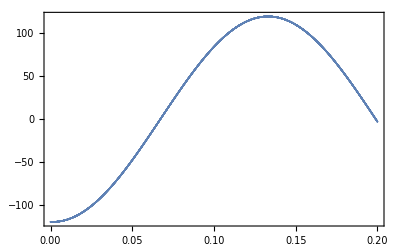

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
tdfunction[td,9]
```

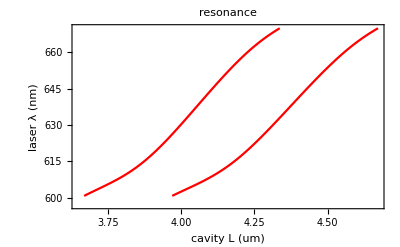

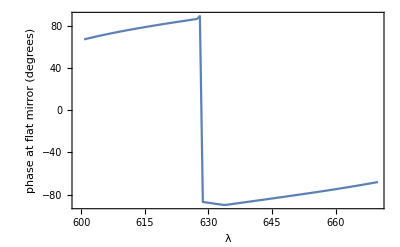

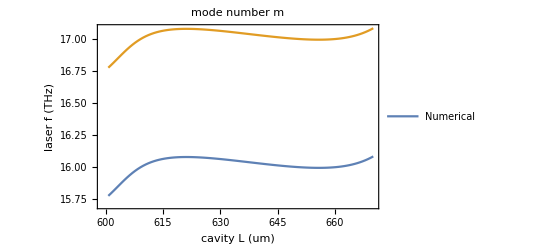

```mathematica
n1 = ListLinePlot[{Transpose[{Lvec1*10^6,λvec*10^9}],Transpose[{Lvec2*10^6,λvec*10^9}]},FrameLabel->{"cavity L (um)","laser λ (nm)"},Frame->True,BaseStyle->{FontFamily->"Arial",FontSize->14},(*PlotMarkers->{Automatic,12},*)FrameStyle->{Black,Directive[Black,FontColor->Black]},PlotStyle->Red,PlotLabel->"resonance"] ;

mcheck = ListLinePlot[{Transpose[{λvec*10^9,2*((nd-1)*td+Lvec1)/λvec-1/2}],Transpose[{λvec*10^9,2*((nd-1)*td+Lvec2)/λvec-1/2}]},FrameLabel->{"cavity L (um)","laser f (THz)"},Frame->True,BaseStyle->{FontFamily->"Arial",FontSize->14},(*PlotMarkers->{Automatic,12},*)FrameStyle->{Black,Directive[Black,FontColor->Black]},PlotLegends->{"Numerical"},PlotLabel->"mode number m"];

phase= ListLinePlot[{Transpose[{λvec*10^9,ArcSin[Ephase/Emax]*180/Pi}]},FrameLabel->{"λ","phase at flat mirror (degrees)"},Frame->True,BaseStyle->{FontFamily->"Arial",FontSize->14},(*PlotMarkers->{Automatic,12},*)FrameStyle->{Black,Directive[Black,FontColor->Black]}];

Print[Show[n1]];
Print[Show[phase]];
Show[mcheck]
```

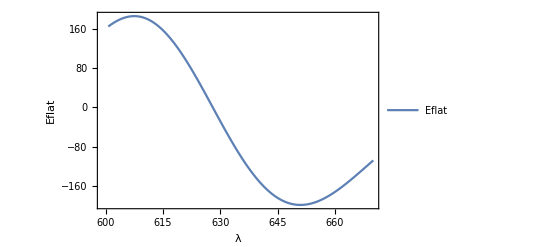

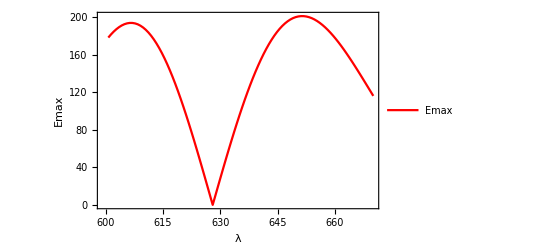

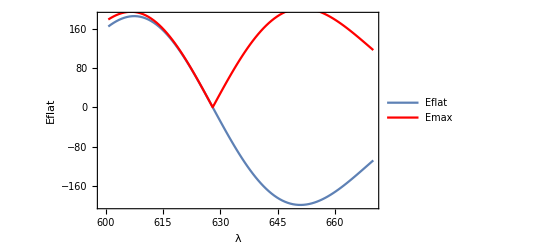

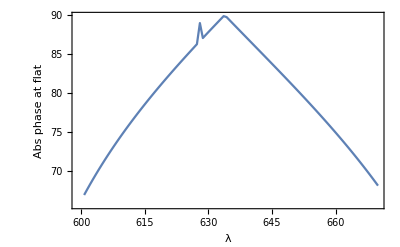

```mathematica
eflat1=ListLinePlot[{Transpose[{λvec*10^9,Ephase}]},FrameLabel->{"λ","Eflat"},Frame->True,BaseStyle->{FontFamily->"Arial",FontSize->14},(*PlotMarkers->{Automatic,12},*)FrameStyle->{Black,Directive[Black,FontColor->Black]},PlotLegends->{"Eflat"}]
emax1=ListLinePlot[{Transpose[{λvec*10^9,Emax}]},FrameLabel->{"λ","Emax"},Frame->True,BaseStyle->{FontFamily->"Arial",FontSize->14},(*PlotMarkers->{Automatic,12},*)FrameStyle->{Black,Directive[Black,FontColor->Black]},PlotLegends->{"Emax"},PlotStyle->Red]
Show[eflat1,emax1]
ListLinePlot[{Transpose[{λvec*10^9,ArcSin[Abs[Ephase/Emax]]*180/Pi}]},FrameLabel->{"λ","Abs phase at flat"},Frame->True,BaseStyle->{FontFamily->"Arial",FontSize->14},(*PlotMarkers->{Automatic,12},*)FrameStyle->{Black,Directive[Black,FontColor->Black]}]
```